```mathematica
Remove["Global`*"];Off[General::spell1]
```

```mathematica
(*
<<Statistics`NormalDistribution`
<<Graphics`Graphics
*)
```

```mathematica
ndist=NormalDistribution[0,1]
```

NormalDistribution[0,1]

```mathematica
pdf = PDF[ndist,x]
```

(ⅇ^(-x^2/2))/(√(2 π))

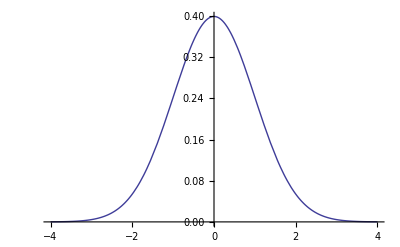

```mathematica
Plot[pdf,{x,-4,4}]
```

```mathematica
∫_(-∞)^∞ pdf ⅆ x
```

1

```mathematica
CDF[ndist,-2]
```

1/2 (1-Erf[√2])

```mathematica
CDF[ndist,-2]//N
```

0.0227501

```mathematica
CDF[ndist,0]//N
```

0.5

```mathematica
Solve[CDF[ndist,y]==p,y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→√2 InverseErf[-1+2 p]}}

```mathematica
Solve[CDF[ndist,y]==1,y]//N
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→∞}}

```mathematica
?Random
```

RowBox[{"Random", "[", "]"}] gives a uniformly distributed pseudorandom Real in the range 0 to 1. 
RowBox[{"Random", "[", RowBox[{StyleBox["type", "TI"], ",", StyleBox["range", "TI"]}], "]"}] gives a pseudorandom number of the specified type, lying in the specified range. Possible types are: Integer, Real and Complex. The default range is 0 to 1. You can give the range RowBox[{"{", RowBox[{StyleBox["min", "TI"], ",", StyleBox["max", "TI"]}], "}"}] explicitly; a range specification of StyleBox["max", "TI"] is equivalent to RowBox[{"{", RowBox[{"0", ",", StyleBox["max", "TI"]}], "}"}].

```mathematica
v=Table[Random[],{1000}];
```

```mathematica
Length[v]
```

1000

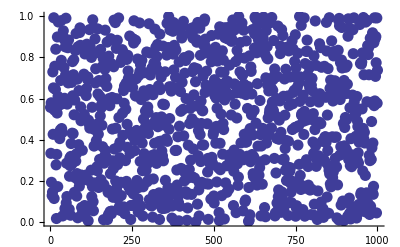

```mathematica
ListPlot[v,PlotStyle->PointSize[0.02]]
```

```mathematica
<<Graphics`Graphics`
```

General::obspkg: Graphics`Graphics` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
Histogram[v,HistogramCategories->100];
```

```mathematica
vn = Table[√2 InverseErf[0,-1+2 v[[i]] ], {i,Length[v]}];
```

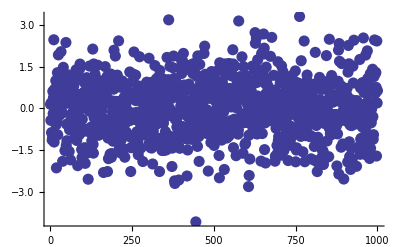

```mathematica
ListPlot[vn,PlotStyle->PointSize[0.02]]
```

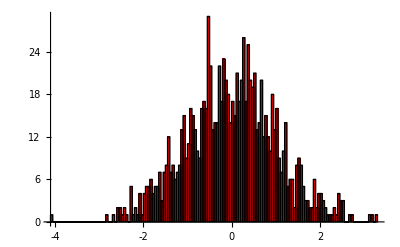

```mathematica
Histogram[vn,HistogramCategories->150]
```

```mathematica
Options[Histogram]
```

{ApproximateIntervals→Automatic,BarEdges→True,BarEdgeStyle→GrayLevel[0],BarOrientation→Vertical,BarStyle→Automatic,FrequencyData→False,HistogramCategories→Automatic,HistogramRange→Automatic,HistogramScale→Automatic,AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,Epilog→{},Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{},DisplayFunction:>$DisplayFunction,FormatType:>TraditionalForm}

```mathematica
∫_(-∞)^∞ ⅇ^(-x^2)ⅆx
```

√π

```mathematica
f[x_,σ_,μ_]:=1/(2 √π σ)ⅇ^(-((x-μ)/(2σ))^2)
```

```mathematica
Assuming[σ>0,∫_(-∞)^∞ f[x,σ,μ]ⅆx]
```

1

```mathematica
∫_(μ-5σ)^(μ+5σ) f[x,σ,μ]ⅆx//N
```

0.999593

```mathematica
r0 = { σ->1,μ->0};
```

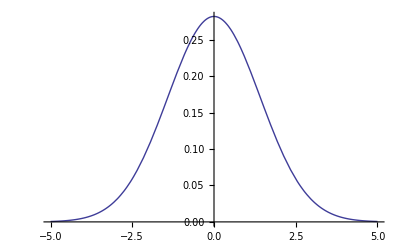

```mathematica
Plot[f[x,σ,μ]/.r0,{x,-5,5}]
```

```mathematica
Plot[∫_(-∞)^t (f[x,σ,μ]/.r0)ⅆx,{t,-5,5}]
```

⁃Graphics⁃

```mathematica
f[x_,σ_,μ_]:=1/(2 √π σ)ⅇ^(-((x-μ)/(2σ))^2)
```

```mathematica
F[x_,σ_,μ_]:=∫_(-∞)^x f[u,σ,μ]ⅆu
```

```mathematica
r0 = { σ->1,μ->0};
```

```mathematica
g={
Plot[{(f[x,σ,μ]/.r0)},{x,-5,5},{DisplayFunction->Identity}],
Plot[Evaluate[F[x,σ,μ]/.r0],{x,-5,5},{DisplayFunction->Identity}]
};
```

```mathematica
Show[g,DisplayFunction->$DisplayFunction]
```

⁃Graphics⁃

```mathematica
r1={μ->100 10^3,σ->0.01 μ};
r2={μ->100 10^3,σ->0.01 μ};
```

```mathematica
n=10000;
v1 = Table[Random[],n]; 
v2 =Table[Random[],n];
```

Table::itform: Argument n at position 2 does not have the correct form for an iterator. More…

```mathematica
u[p_,σ_,μ_]:=Assuming[σ>0,Solve[F[x,σ,μ]==p,x]]
```

```mathematica
vn = Table[√2 InverseErf[0,-1+2 v[[i]] ], {i,Length[v]}];
```

```mathematica
u[p_,σ_,μ_]:=Assuming[σ>0,Solve[F[x,σ,μ]==p,x]]
```